```mathematica
StartTime = AbsoluteTime[];

(****************************************)
(******* Piecewise[{{F[μ(t), τ(t), t] = 0, □}, {τ=∫_a^t μ(ξ)K(ξ,t)ⅆξ, □}}] ********)
(****************************************)

(*Functions and constants*)
a=0; (*Bounds*)
b=2;

F[u_,v_,t_]=t+u+v^3; (* Functions *)
K[ξ_,t_]=Log[(ξ-t)^2+1]^2;

dFu[u_,v_,t_]=D[F[u,v,t],u]; (* Partial derivatives*)
dFv[u_,v_,t_]=D[F[u,v,t],v];

(* Accuracy *)
eps=10^(-12); 
(* Number of nodes *)
NN=10;
(*Grid*)
UniformGrid = Table[i,{i,a,b,(b-a)/(NN-1)}]; 
(*Number of max iterations*)
MAXITER=30;

(*Print["Grid\n", MatrixForm[UniformGrid]];*)
```

```mathematica
(*****************************************)
(*Matrix of weight coeffs.*)
Dw=Table[0.0,{i,1,NN},{l,1,NN}];
(*Filling matrix Dw*)
For[j=1,j<=NN,j++,
(*Preparation for the natural spline making*)
w=Table[{UniformGrid[[k]],0.0},{k,1,NN}]; (*Pairs of values {grid point, function values}*)
w[[j,2]]=1; (*Definition of natural spline as a spline through only 1 nodes with value 1 and others are 0*)(*Interpolation polynom*)
S=Interpolation[w];
For[i=1,i<NN,i++,
Dw[[i+1,j]]=Dw[[i,j]]+Integrate[S[x],{x,UniformGrid[[i]],UniformGrid[[i+1]]}];
];
];
(*****************************************)
(*Print["Dw/n", MatrixForm[Dw]];*)
```

```mathematica
(******* Initial solution *********)
μ=Table[1.0,{NN}];

(* "Stiffness" matrix *)
TT=Table[Dw[[i,j]]*K[UniformGrid[[j]],UniformGrid[[i]]],{i,1,NN},{j,1,NN}];
NormMax=1;
kk=0;
```

```mathematica
While[NormMax>=eps,
τ=TT.μ;
Lhs=Table[
If[i!=j,
dFv[μ[[i]],τ[[i]],UniformGrid[[i]]]*TT[[i,j]],
dFv[μ[[i]],τ[[i]],UniformGrid[[i]]]*TT[[i,j]]+dFu[μ[[i]],τ[[i]],UniformGrid[[i]]]
],
{i,1,NN},{j,1,NN}];
Rhs=Table[-F[μ[[i]],τ[[i]],UniformGrid[[i]]],{i,1,NN}];
(*Print["Lhs\n", MatrixForm[Lhs]];*)
(*Print["Rhs\n", MatrixForm[Rhs]];*)
deltamu=LinearSolve[Lhs,Rhs];
μ=μ+deltamu;
NormMax=Max[Abs[Rhs]];
kk++;
Print["Iteration: ",kk];
Print["Норма по максимальному отклонению: |b|_{max}=", NormMax];
Print["Вторая норма невязки: |b|_{2}=", Sqrt[Rhs.Rhs]];
If[kk>=MAXITER,Break[]];
]
```

Iteration: 1

Норма по максимальному отклонению: |b|_{max}=6.7516

Вторая норма невязки: |b|_{2}=9.48173

Iteration: 2

Норма по максимальному отклонению: |b|_{max}=12.0327

Вторая норма невязки: |b|_{2}=12.5474

Iteration: 3

Норма по максимальному отклонению: |b|_{max}=0.000317684

Вторая норма невязки: |b|_{2}=0.0003177

Iteration: 4

Норма по максимальному отклонению: |b|_{max}=1.11022×10^-16

Вторая норма невязки: |b|_{2}=1.54714×10^-16

0. | 0.
0. | 3.3888×10^-10
0. | -7.19431×10^-10
0. | -8.95841×10^-8
0. | -1.92329×10^-6
0. | -9.17968×10^-6
0. | -0.0000121952
0. | -0.000211204
0. | -0.00125127
0. | -0.00410134
0. | 0.00387497
0. | 0.000288525

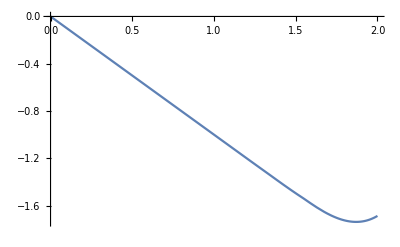

```mathematica
(* Просмотр решения *)
funcmu=Interpolation[Table[{UniformGrid[[i]],μ[[i]]},{i,1,NN}]];

SolutionCheck=Table[{0.,F[funcmu[t],NIntegrate[funcmu[x]*K[x,t],{x,a,t}],t]},{t,a,b,(b-a)/11}];
SolutionCheck//TableForm
Plot[funcmu[x],{x,a,b},PlotRange->All]
```

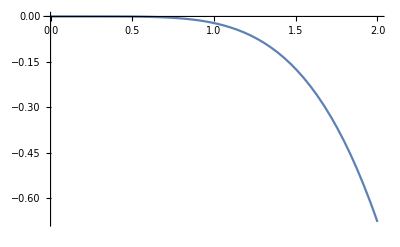

```mathematica
functau[t_]:=Integrate[funcmu[z]*K[z,t],{z,a,t}]
Plot[functau[y],{y,a,b},PlotRange->All]
```